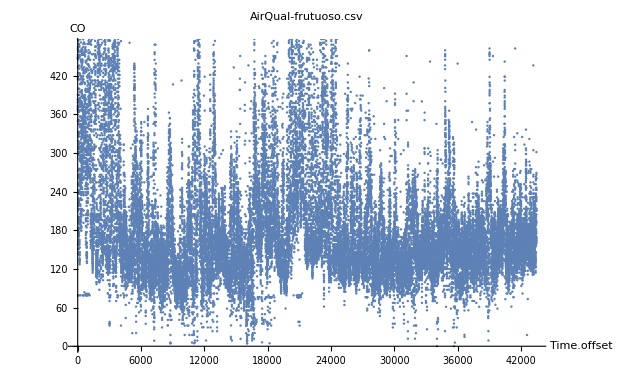

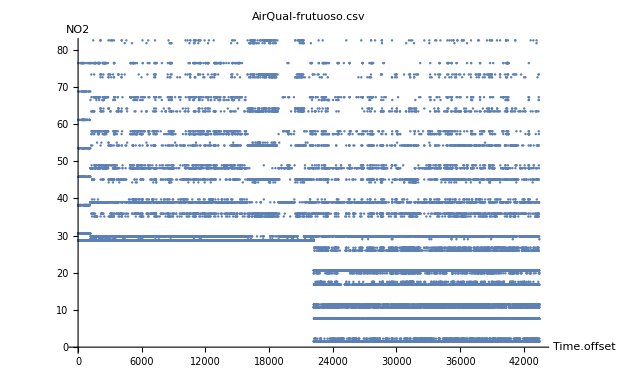

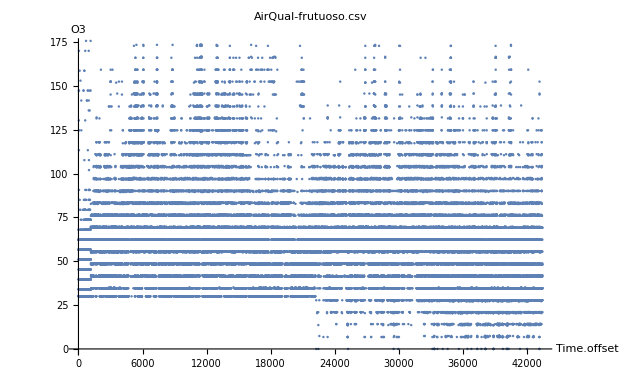

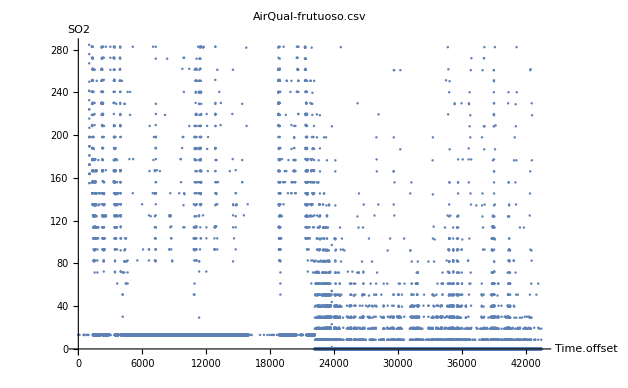

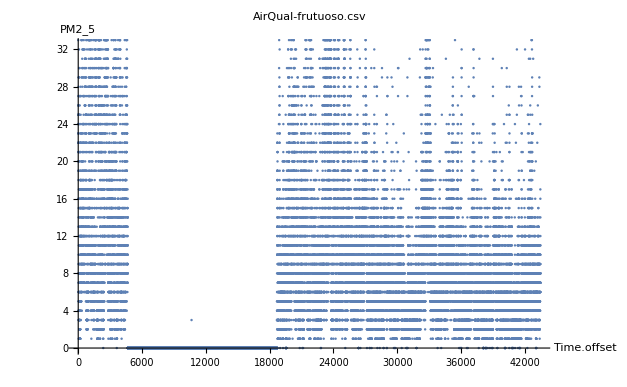

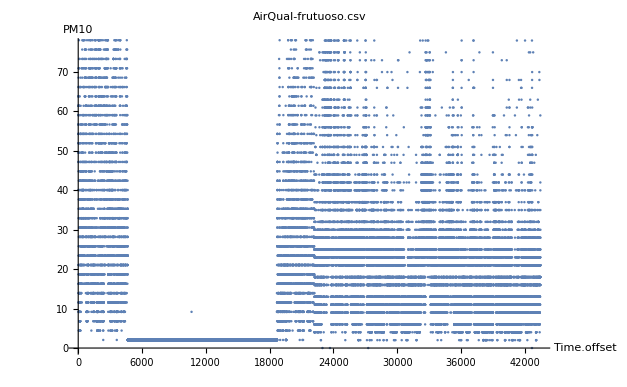

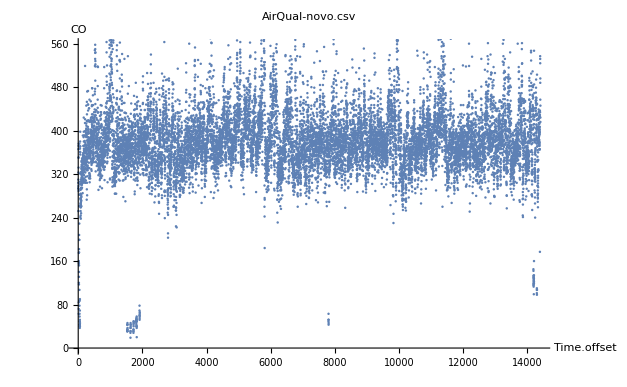

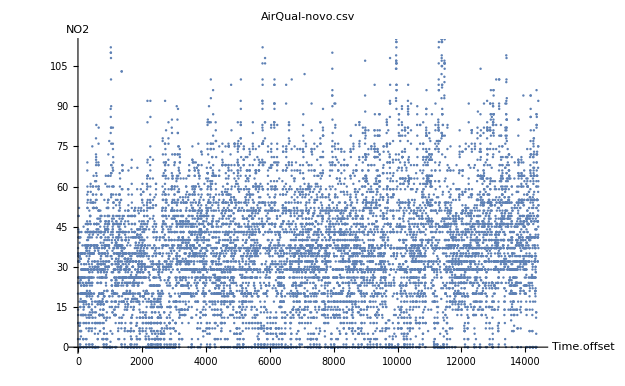

```mathematica
ClearAll["Global`*"]

fitTimeseriesModel[f_,y_,z_]:=Module[{fname=f,yaxis=y,colnum=z},
dataset=Import[StringJoin["/home/david/Documents/digital-twins/d4fa/HistoriAirQual/",fname],{"CSV","Data",All,{1,z}},"HeaderLines"->1,"FieldSeparators"->",",MissingDataRules->{"."->Missing[],""->Missing[]}];
time=dataset[[All,1]];
time=Subtract[time,time[[1]]];
timeseries=TimeSeries[dataset[[All,2]],{time}]; (* is 2 because only 2 data columns read *)
Print[ListPlot[dataset[[All,2]],PlotLabel->fname,AxesLabel->{"Time.offset",yaxis}]];
(*atsm=TimeSeriesModelFit[timeseries];
process=Normal[atsm];
Print[process];
Print[CovarianceFunction[process,s,t]];
Print[TimeSeriesForecast[process,dataset[[All,2]], 2]];
*)
];
(***********************************************)
 (* utc_timestamp, datahora, local, CO, NO2, O3, SO2, PM2_5, PM10, noise_db *)
fitTimeseriesModel["AirQual-frutuoso.csv","CO",4]; 
fitTimeseriesModel["AirQual-frutuoso.csv","NO2",5];fitTimeseriesModel["AirQual-frutuoso.csv","O3",6];
fitTimeseriesModel["AirQual-frutuoso.csv","SO2",7];
fitTimeseriesModel["AirQual-frutuoso.csv","PM2_5",8]; 
fitTimeseriesModel["AirQual-frutuoso.csv","PM10",9]; 

fitTimeseriesModel["AirQual-novo.csv","CO",4];
fitTimeseriesModel["AirQual-novo.csv","NO2",5];
fitTimeseriesModel["AirQual-novo.csv","O3",6];
fitTimeseriesModel["AirQual-novo.csv","SO2",7];
fitTimeseriesModel["AirQual-novo.csv","PM2_5",8]; 
fitTimeseriesModel["AirQual-novo.csv","PM10",9]; 

fitTimeseriesModel["AirQual-rotunda.csv","CO",4];
fitTimeseriesModel["AirQual-rotunda.csv","NO2",5];
fitTimeseriesModel["AirQual-rotunda.csv","O3",6];
fitTimeseriesModel["AirQual-rotunda.csv","SO2",7];
fitTimeseriesModel["AirQual-rotunda.csv","PM2_5",8]; 
fitTimeseriesModel["AirQual-rotunda.csv","PM10",9]; 

fitTimeseriesModel["AirQual-forum.csv","CO",4];
fitTimeseriesModel["AirQual-forum.csv","NO2",5];
fitTimeseriesModel["AirQual-forum.csv","O3",6];
fitTimeseriesModel["AirQual-forum.csv","SO2",7];
fitTimeseriesModel["AirQual-forum.csv","PM2_5",8]; 
fitTimeseriesModel["AirQual-forum.csv","PM10",9]; 
(***********************************************)
```